## Inicialize some functions

```mathematica
<<CompiledFunctionTools`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
```

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=5;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
(*{{3,-1/2,√(3/5)},{4,-0.333,0.756},{5,-0.2501,0.7454},{6,-0.2,0.738},{7,-0.173,0.7346},{8,-0.14,0.73},{9,-0.1255,0.7277},{10,-0.1111,0.7255},{11,-0.1,0.7238},{12,-0.09,0.7223},{13,-0.0834,0.7211},{14,-0.0769,0.72}};*)
{c1,c2}={-0.2501,0.7454};
(*{c1,c2}={-1/2,√(3/5)};*)
derPiece[λ_?NumericQ,χ_?NumericQ]:=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-0.3,1.2},{χ,0,0.9},ScalingFunctions->"Log10",PlotPoints->20];
```

```mathematica
tmaxI=10;
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solMulti=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[θ],Sin[θ]]],{λ,χ},{t,0,tmaxI},PrecisionGoal->2,AccuracyGoal->2,WorkingPrecision->10],{θ,0,π/2,π/30}];
solMulti1=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[θ],Sin[θ]]],{λ,χ},{t,0,tmaxI}],{θ,0,π/2,π/30}];
solMulti2=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[θ],Sin[θ]]],{λ,χ},{t,0,tmaxI},Method->"ExplicitRungeKutta"],{θ,0,π/2,π/30}];
```

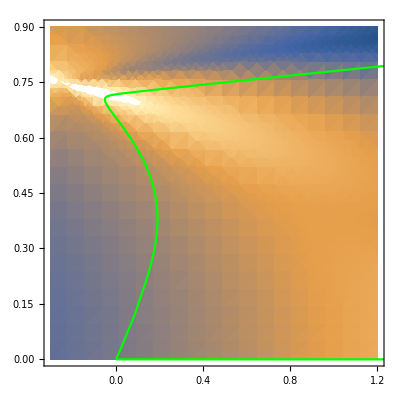

```mathematica
geodInitial=ParametricPlot[{λ[t],χ[t]}/.solMulti,{t,0,tmaxI},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
geodInitial=ParametricPlot[{λ[t],χ[t]}/.solMulti1,{t,0,tmaxI},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
geodInitial=ParametricPlot[{λ[t],χ[t]}/.solMulti2,{t,0,tmaxI},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
```

```mathematica
solMulti1=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[θ],Sin[θ]]],{λ,χ},{t,0,tmaxI}],{θ,0,π/3,π/30}];
```

# Output

```mathematica
solMulti
```

```mathematica
solMulti1
```

```mathematica
solMulti2
```